```mathematica
SetDirectory[NotebookDirectory[]];
CreateDirectory[FileNameJoin[{NotebookDirectory[],"output","figure"}]]
```

/Users/kumaryu/Dropbox/project/Seasonal phase/simulation_public/output/figure

```mathematica
<<MaTeX`
```

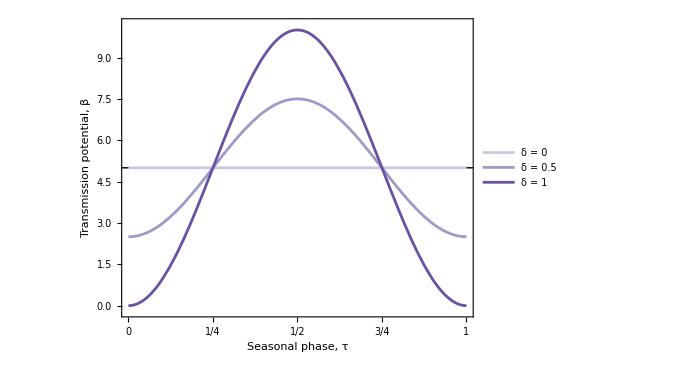

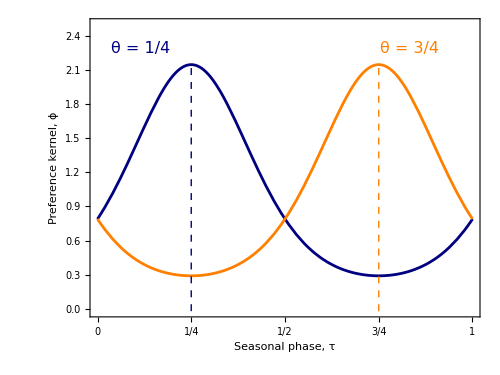

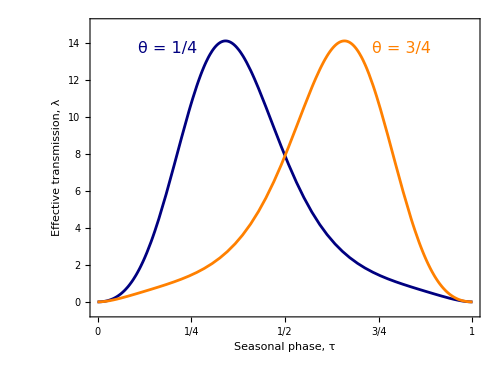

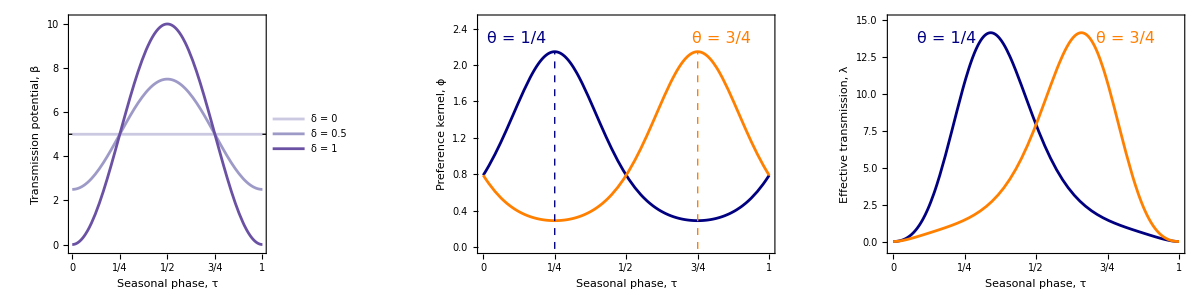

```mathematica
tauTickstate={{0,"0"},{1/4,"1/4"},{1/2,"1/2"},{3/4,"3/4"},{1,"1"}};
tauTicks={{0,"0"},{1/4,"1/4"},{1/2,"1/2"},{3/4,"3/4"},{1,"1"}};
IS=500;
βcolor={RGBColor["#bae4b3"],RGBColor["#74c476"],RGBColor["#238b45"]};
βcolor={RGBColor["#fcae91"],RGBColor["#fb6a4a"],RGBColor["#cb181d"]};
βcolor={RGBColor["#fdbe85"],RGBColor["#fd8d3c"],RGBColor["#d94701"]};
βcolor={RGBColor["#cbc9e2"],RGBColor["#9e9ac8"],RGBColor["#6a51a3"]};






p1=Plot[{5,5(1+0.5 Cos[2π(τ-1/2)]),5(1+Cos[2π(τ-1/2)])},{τ,0,1},Frame->True,FrameLabel->{Style["Seasonal phase, τ",20],Style["Transmission potential, β",20]},PlotRange->{-0.2,10.2},Axes->None,AspectRatio->3/4,PlotLegends->Placed[{Style["δ = 0",14],Style["δ = 0.5",14],Style["δ = 1",14]}, Scaled[{0.85,0.8}]],FrameTicks->{{Automatic,Automatic},{tauTicks,None}},GridLines->None,FrameStyle->Directive[Black,15],PlotRangePadding->None,ImagePadding->{{50,0},{50,10}},ImageSize->{IS,Automatic},Prolog->{Line[{{-π,5},{π,5}}]},PlotStyle->βcolor]

p2=Plot[{(1/(BesselI[0,1]))*Exp[1 Cos[2 Pi (τ-1/4)]],(1/(BesselI[0,1]))*Exp[Cos[2 Pi (τ-3/4)]]},{τ,0,1},Frame->True,FrameLabel->{Style["Seasonal phase, τ",20],Style["Preference kernel, ϕ",20]},AspectRatio->3/4,PlotRange->{-0.02,2.5},FrameStyle->Directive[Black,15],Axes->None,FrameTicks->{{Automatic,Automatic},{tauTicks,None}},PlotStyle->{RGBColor["#000080"],Orange},GridLines->None,ImageSize->{IS,Automatic},PlotRangePadding->None,ImagePadding->{{50,0},{50,10}},Epilog->{Dashed,RGBColor["#000080"],Line[{{1/4,-0.02},{1/4,ⅇ/BesselI[0,1]}}],Dashed,Orange,Line[{{3/4,-0.02},{3/4,Exp[1]/BesselI[0,1]}}],RGBColor["#000080"],Text[Style["θ = 1/4",16],Scaled[{0.13,0.9}]],Orange,Text[Style["θ = 3/4",16],Scaled[{0.82,0.9}]]}]

p3=Plot[{(1/(BesselI[0,1]))*Exp[1 Cos[2 Pi (τ-1/4)]]*5(1+1*Cos[2π(τ-1/2)]),(1/(BesselI[0,1]))*Exp[Cos[2 Pi (τ-3/4)]]5(1+1*Cos[2π(τ-1/2)])},{τ,0,1},Frame->True,PlotRange->{-0.5,15},FrameLabel->{Style["Seasonal phase, τ",20],Style["Effective transmission, λ",20]},AspectRatio->3/4,FrameStyle->Directive[Black,15],Axes->None,FrameTicks->{{Automatic,Automatic},{tauTicks,None}},PlotStyle->{RGBColor["#000080"],Orange},GridLines->None,ImageSize->{IS,Automatic},PlotRangePadding->None,ImagePadding->{{50,0},{50,10}},Epilog->{RGBColor["#000080"],Text[Style["θ = 1/4",16],Scaled[{0.2,0.9}]],Orange,Text[Style["θ = 3/4",16],Scaled[{0.8,0.9}]]}]

P1ABC=GraphicsRow[{p1,p2,p3},ImageSize->{1200,300}]
```

```mathematica
τ[t_]:=Mod[t,1]
invPrincipal[τ_]:=(τ+Pi)/(2 Pi);
ClearAll[vonMisesPDF]
vonMisesPDF[x_,μ_,κ_]:=(1/(BesselI[0,κ]))*Exp[κ Cos[2π(x-μ)]]
dϕ=D[ vonMisesPDF[τ[t],θ,k],θ]//Simplify
subβ={β->β0*(1+δ*Cos[2π(t-1/2)])};
subϕ={ϕ->vonMisesPDF[τ[t],θ,k]};
ρ[z_]:=β*s*vonMisesPDF[τ[t],θ,k]-(d+γ+α)/.subβ/.θ->z
ds=d*(s+j+r)-d*s+c*r-β*s*ϕ*j;
dj=(β*s*ϕ-(d+γ+α))*j;
dr=γ*j-d*r-c*r;
subvarfvz={s->s[t],j->j[t],r->r[t]};
```

(2 ⅇ^(k Cos[2 π (-θ+Mod[t,1])]) k π Sin[2 π (-θ+Mod[t,1])])/BesselI[0,k]

1/4

3/4

1/2

{d→0.1,γ→1,α→0,c→0.5,k→1,β0→5,δ→1,vm→0.}

{s[0]==0.99,j[0]==0.01,r[0]==0}

1000

{{s→InterpolatingFunction[{{0., 1000.}}, <>],j→InterpolatingFunction[{{0., 1000.}}, <>],r→InterpolatingFunction[{{0., 1000.}}, <>]}}

{{s→InterpolatingFunction[{{0., 1000.}}, <>],j→InterpolatingFunction[{{0., 1000.}}, <>],r→InterpolatingFunction[{{0., 1000.}}, <>]}}

{{s→InterpolatingFunction[{{0., 1000.}}, <>],j→InterpolatingFunction[{{0., 1000.}}, <>],r→InterpolatingFunction[{{0., 1000.}}, <>]}}

{InterpolatingFunction[{{0., 1000.}}, <>][999+x],InterpolatingFunction[{{0., 1000.}}, <>][999+x],InterpolatingFunction[{{0., 1000.}}, <>][999+x]}

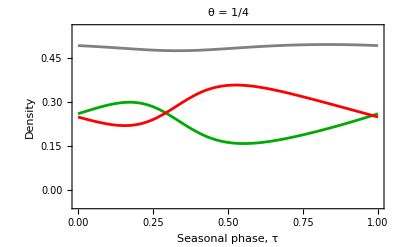

{InterpolatingFunction[{{0., 1000.}}, <>][999+x],InterpolatingFunction[{{0., 1000.}}, <>][999+x],InterpolatingFunction[{{0., 1000.}}, <>][999+x]}

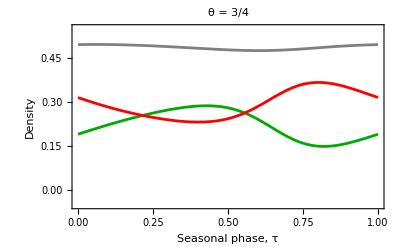

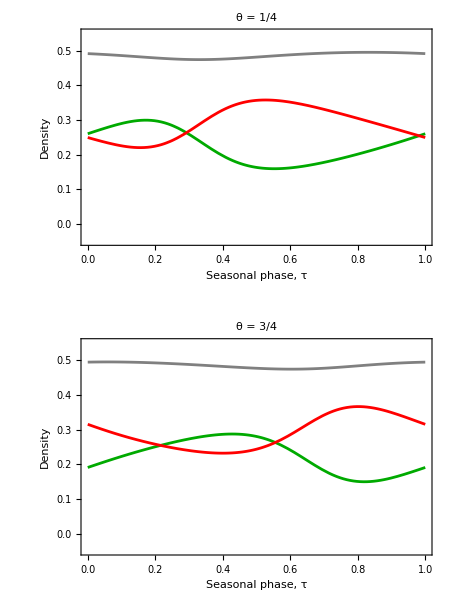

```mathematica
(*区間*)t1=999;t2=1000;
θv=1/4
θv2=3/4
θv3=1/2
  par={d->0.1,γ->1,α->0,c->0.5,k->1,β0->5,δ->1,vm->0.}
initfvz={s[0]==1-0.01,j[0]==0.01,r[0]==0}
dynfvz={s'[t]==(ds/.subβ/.subϕ/.subvarfvz),j'[t]==(dj/.subβ/.subϕ/.subvarfvz),r'[t]==(dr/.subβ/.subϕ/.subvarfvz)};
sysfvz=Join[dynfvz,initfvz];
tend=1000
sol=NDSolve[Evaluate[{sysfvz/.par/.θ->θv}],{s,j,r},{t,0,tend},Method->{"FixedStep",Method->"ExplicitEuler","StepSize"->0.01}]
sol2=NDSolve[Evaluate[{sysfvz/.par/.θ->θv2}],{s,j,r},{t,0,tend},Method->{"FixedStep",Method->"ExplicitEuler","StepSize"->0.01}]
sol3=NDSolve[Evaluate[{sysfvz/.par/.θ->θv3}],{s,j,r},{t,0,tend},Method->{"FixedStep",Method->"ExplicitEuler","StepSize"->0.01}]
ttau[tau_]:=t1+tau
S[t_]:=s/.subβ/.subϕ/.subvarfvz/.par/.θ->θv/.sol[[1]];(*your S(t)*);
S2[t_]:=s/.subβ/.subϕ/.subvarfvz/.par/.θ->θv2/.sol2[[1]];(*your S(t)*);
S3[t_]:=s/.subβ/.subϕ/.subvarfvz/.par/.θ->θv3/.sol3[[1]];(*your S(t)*);
J[t_]:=j/.subβ/.subϕ/.subvarfvz/.par/.θ->θv/.sol[[1]];(*your S(t)*);
J2[t_]:=j/.subβ/.subϕ/.subvarfvz/.par/.θ->θv2/.sol2[[1]];(*your S(t)*);
J3[t_]:=j/.subβ/.subϕ/.subvarfvz/.par/.θ->θv3/.sol3[[1]];(*your S(t)*);
R[t_]:=r/.subβ/.subϕ/.subvarfvz/.par/.θ->θv/.sol[[1]];(*your S(t)*);
R2[t_]:=r/.subβ/.subϕ/.subvarfvz/.par/.θ->θv2/.sol2[[1]];(*your S(t)*);
R3[t_]:=r/.subβ/.subϕ/.subvarfvz/.par/.θ->θv3/.sol3[[1]];(*your S(t)*);

{S[t],J[t],R[t]}/.t->ttau[x]
p4=Plot[%,{x,0,1},FrameStyle->Directive[12,Black],Frame->True,PlotRange->{-0.05,0.55},FrameLabel->{Style["Seasonal phase, τ",20],Style["Density",20]},PlotStyle->{Darker[Green],Red,Gray},PlotLabel->Style["θ = 1/4",Black,18]]

{S2[t],J2[t],R2[t]}/.t->ttau[x]
p5=Plot[%,{x,0,1},FrameStyle->Directive[12,Black],Frame->True,PlotRange->{-0.05,0.55},FrameLabel->{Style["Seasonal phase, τ",20],Style["Density",20]},PlotStyle->{Darker[Green],Red,Gray},PlotLabel->Style["θ = 3/4",Black,18]]
PLL=LineLegend[{Darker[Green],Red,Gray},{Style["Susceptible",16],Style["Infected",16],Style["Recovered",16]}]


P1DE=GraphicsColumn[{p4,p5},ImageSize->{450,600}]
```

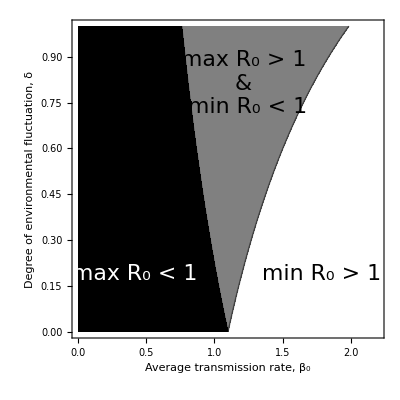

```mathematica
vonMisesPDF[x_,μ_,κ_]:=(1/(BesselI[0,κ]))*Exp[κ Cos[2π(x-μ)]]
subβ={β->β0*(1+δ*Cos[2π(t-1/2)])};
subϕ={ϕ->vonMisesPDF[t,θ,k]};
 Funcmax[β0v_,δv_]:= NIntegrate[β ϕ-(d+γ)/.subβ/.subϕ/.{d->0.1,γ->1,α->0,c->0.5,k->1,vm->0.}/.θ->1/2/.β0->β0v/.δ->δv,{t,0,1}]
Funcmin[β0v_,δv_]:= NIntegrate[β ϕ-(d+γ)/.subβ/.subϕ/.{d->0.1,γ->1,α->0,c->0.5,k->1,vm->0.}/.θ->0/.β0->β0v/.δ->δv,{t,0,1}]
ContourPlot[{Funcmax[β0,δ]},{β0,0,2.2},{δ,0,1},Contours->{0},ContourShading->{Black,None}];
ContourPlot[{Funcmin[β0,δ]},{β0,0,2.2},{δ,0,1},Contours->{0},ContourShading->{Gray,None}];
P1C=Show[{%,%%},FrameStyle->Directive[Black,12],ImageSize->{Automatic,400},FrameLabel->{Style["Average transmission rate, β_0",22],Style["Degree of environmental fluctuation, δ",22]},Epilog->{Text[Style["max R_0 < 1",White,22],Scaled[{0.2,0.2}]],Text[Style["max R_0 > 1\n&\n min R_0 < 1",Black,22],Scaled[{0.55,0.8}]],Text[Style["min R_0 > 1",Black,22],Scaled[{0.8,0.2}]]}]
P1C=Rasterize[P1C,"Image",ImageResolution->300,ImageSize->500];
```

```mathematica
PDEF=GraphicsRow[{Labeled[P1DE,PLL,Right,Spacings->0],P1C},ImageSize->{1250,650},Method->{"TransparentPolygonMesh"->True}]
GraphicsColumn[{P1ABC,PDEF},ImageSize->{1250,1000},Epilog->{Text[Style["A",20],Scaled[{0.07,0.99}]],Text[Style["B",20],Scaled[{0.36,0.99}]],Text[Style["C",20],Scaled[{0.65,0.99}]],Text[Style["D",20],Scaled[{0.08,0.63}]],Text[Style["E",20],Scaled[{0.08,0.33}]],Text[Style["F",20],Scaled[{0.55,0.6}]]}]
Export["output/figure/Fig1_revise.pdf",%]
```

-Graphics-

-Graphics-

output/figure/Fig1_revise.pdf

```mathematica
evoP=　 Rest@ Import["output/evo_points.tsv","Table"];
unstablelist={};
stablelist={};
branchlist={};
Do[If[i[[3]]=="repeller",
AppendTo[unstablelist,{i[[2]],i[[1]]}],If[i[[3]]=="CSS",AppendTo[stablelist,{i[[2]],i[[1]]}],AppendTo[branchlist,{i[[2]],i[[1]]}]]],
{i,evoP}]
```

0.0507813

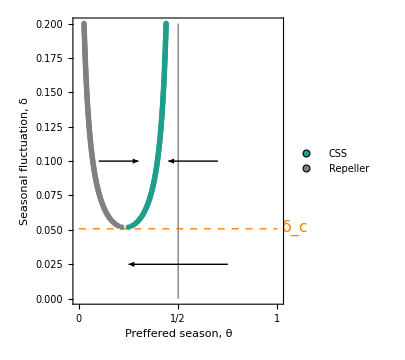

```mathematica
δcv=0.05078125
P1=ListPlot[{stablelist,unstablelist},Frame->True,Axes->False,PlotRange->{{0-0.01,1+0.01},{0,0.2}},PlotMarkers->{{Graphics[{RGBColor["#1F9E89"],Disk[]}],0.02},{Graphics[{Gray,Disk[]}],0.02}},AspectRatio->1.2,Axes->False,FrameTicks->{Automatic,{tauTicks,None}},Prolog->{Gray,Line[{{0.5,0},{0.5,0.2}}],Dashed,Orange,Line[{{0,δcv},{1,δcv}}]},
Epilog->{Inset[Style["δ_c",16,Orange],Scaled[{1.05,0.265}]],Arrow[{{0.1,0.1},{0.3,0.1}}],Arrow[{{0.7,0.1},{0.45,0.1}}],Arrow[{{3/4,0.025},{1/4,0.025}}]},
PlotRangeClipping->False,
FrameStyle->Directive[Black,12],FrameLabel->{Style["Preffered season, θ",15],Style["Seasonal fluctuation, δ",15]},ImageSize->300,ImagePadding->{{50,20},{40,5}},PlotRangePadding->None,PlotLegends->Placed[{Style["CSS",15],Style["Repeller",15]},Scaled[{0.8,0.85}]]]
```

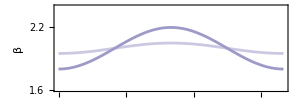

```mathematica
P2=Plot[{2(1+0.025 Cos[2π(τ-1/2)]),2(1+0.1Cos[2π(τ-1/2)])},{τ,0,1},Frame->True,PlotRange->{2-0.4,2+0.4},Axes->None,AspectRatio->1/3,PlotLegends->Placed[{"δ = 0.025","δ = 0.1"}, Scaled[{0.85,0.8}]],FrameLabel->{None,Style["β",15]},FrameTicks->{{{1.6,1.8,2.0,2.2,2.4},Automatic},{None,None}},GridLines->None,FrameStyle->Directive[Black,12],PlotRangePadding->None,ImagePadding->{{50,20},{5,5}},ImageSize->300,Prolog->{Line[{{-π,5},{π,5}}]},PlotStyle->{RGBColor["#cbc9e2"],RGBColor["#9e9ac8"]}]
```

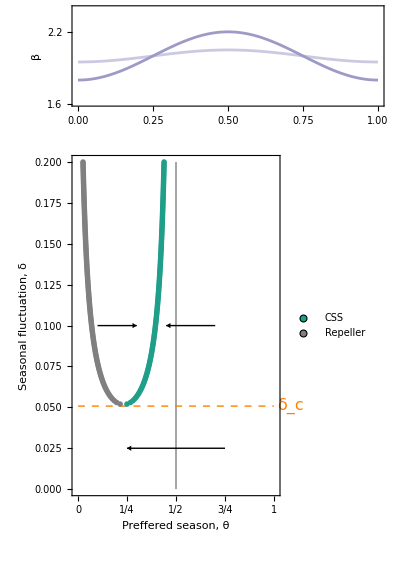

output/figure/Fig3right_revise.pdf

```mathematica
GraphicsColumn[{P2,P1},ImageSize->400]
 Export["output/figure/Fig3right_revise.pdf",%]
```

```mathematica
SGfixed=Rest@Import["output/selection_gradient_0.1.tsv","Table"];
SGfixed=Table[{i[[1]],i[[2]],i[[3]],i[[4]]},{i,SGfixed}];
fixedPLT=ListLinePlot[{SGfixed[[All,{1,2}]],SGfixed[[All,{1,3}]],SGfixed[[All,{1,4}]]},Frame->True,PlotRange->{{0-0.01,1+0.01},{-0.6,0.4}},PlotStyle->{Black,Lighter[Blue],Lighter[Red]},ImagePadding->{{30,1},{20,5}},Epilog->{PointSize->0.02,Gray,Point[{0.06964051450647554,0}],RGBColor["#1F9E89"],Point[{0.395254761661653,0}]},AspectRatio->0.5,Axes->False,PlotLabel->Style["δ = 0.1",Black,15],Prolog->{Gray,Thickness->0.003,Line[{{0,0},{1,0}}]},FrameStyle->Directive[Black,12],(*PlotLegends->Placed[{"𝒮","A_0","A_1"},Scaled[{0.8,0.8}]],*)FrameTicks->{Automatic,{tauTicks,None}}]
SGdrift=Rest@Import["output/selection_gradient_0.01.tsv","Table"];
SGdrift=Table[{i[[1]],i[[2]],i[[3]],i[[4]]},{i,SGdrift}];
driftPLT=ListLinePlot[{SGdrift[[All,{1,2}]],SGdrift[[All,{1,3}]],SGdrift[[All,{1,4}]]},Frame->True,PlotRange->{{0-0.01,1+0.01},{-0.6,0.4}},ImagePadding->{{30,1},{20,5}},PlotStyle->{Black,Lighter[Blue],Lighter[Red]},AspectRatio->0.5,Axes->False,Prolog->{Gray,Thickness->0.003,Line[{{0,0},{1,0}}]},FrameStyle->Directive[Black,12],PlotLabel->Style["δ = 0.01",Black,15],(*PlotLegends->Placed[{"𝒮","A_0","A_1"},Scaled[{0.8,0.8}]],*)FrameTicks->{Automatic,{tauTicks,None}}(*FrameLabel->{Style["Seasonal preference, θ",15],Style["Selection gradient",15]}*)]
leg=LineLegend[{Black,Lighter[Blue],Lighter[Red]},{"𝒮(θ)(=𝒮_0(θ)+𝒮_1(θ)): Selection gradient","𝒮_0(θ):Seasonal priority effect","𝒮_1(θ):Seasonal stabilizing effect"},LegendLayout->"Column",LegendFunction->(Framed[#,FrameStyle->GrayLevel[0],Background->None,FrameMargins->8,RoundingRadius->0]&),LabelStyle->Directive[FontFamily->"Helvetica",14]]
Fig4AB=GraphicsColumn[{ Labeled[GraphicsColumn[{driftPLT,fixedPLT},Spacings->5],{(*Rotate[Style["Selection gradient",15],Pi/2],*)(*左（縦）ラベル*)Style["Preferred season, θ",15]           (*下ラベル*)},{(*Left,*)Bottom},(*配置*)LabelStyle->Directive[FontFamily->"Helvetica",15]],leg},ImageSize->400]
```

```mathematica
Rest@ Import["output/rho_list_figure_0_2.tsv","Table"];
Rest@ Import["output/rho_list_figure_0.1_2.tsv","Table"];
Rest@ Import["output/rho_list_figure_0_2.tsv","Table"];
Table[{i[[1]],i[[2]]},{i,%}];
Pinvmove=ListLinePlot[{%},Frame->True,Axes->{True,False},FrameStyle->Directive[Black,15],AspectRatio->0.5,FrameLabel->{Style["Preffered season, θ",20],Style["Invasion fitness", 20]},FrameTicks->{{{{0,Style["0"]}},None},{tauTicks,None}},Epilog->{Black,PointSize->0.025,Point[{0.5,0}]}]

Rest@ Import["output/rho_list_figure_0.025_2.tsv","Table"];
Table[{i[[1]],i[[2]]},{i,%}];
Pinvmove2=ListLinePlot[{%},Frame->True,Axes->{True,False},FrameStyle->Directive[Black,15],AspectRatio->0.5,FrameLabel->{Style["Preffered season, θ",20],Style["Invasion fitness", 20]},FrameTicks->{{{{0,Style["0"]}},None},{tauTicks,None}},Epilog->{Black,PointSize->0.025,Point[{0.5,0}]}]

Rest@Import["output/rho_list_figure_0.1_2.tsv","Table"];
Table[{i[[1]],i[[2]]},{i,%}];
Pinvstasis=ListLinePlot[{%},Frame->True,Axes->{True,False},PlotRange->{-0.03,0.01},FrameStyle->Directive[Black,15],AspectRatio->0.5,FrameLabel->{Style["Preffered season, θ",20],Style["Invasion fitness", 20]},FrameTicks->{{{{0,Style["0"]}},None},{tauTicks,None}},Epilog->{RGBColor["#1F9E89"],PointSize->0.025,Point[{0.395254761661653,0}]}]
```

```mathematica
bifdata=Rest@Import["output/ES_pattern_long.tsv","Table"];
criticallist=Rest@Import["output/critical_delta_vs_beta.csv","Data"];
criticallisttrue={};
criticallist = Do[If[i[[1]]>1.1&&i[[2]]<0.4,AppendTo[criticallisttrue,{i[[1]],i[[2]]}]],{i,criticallist}]
 ListContourPlot[bifdata,Contours->{0.5,1.5},ContourStyle->None,InterpolationOrder->0,FrameStyle->Directive[Black,12],ContourShading->{LightGray,RGBColor["#1F9E89"],RGBColor["#000080"]},FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]}]
ListLinePlot[{criticallisttrue},PlotStyle->{{Orange,Thickness->0.005}}];
Show[{%%,%},Epilog->{Text[Style["CSS",20],{4,0.3}],Text[Style["No singular point",20],{7,0.1}],Text[Style["Branching",20],{7,0.36},{1,0}],Orange,Text[Style["δ_C",16],{9,0.35},{1,0}],{Black,Thickness->0.002,Line[{{7,0.36},{8.1,0.36}}]}}]
Rasterize[%,"Image",ImageResolution->300];
```

```mathematica
matrixoligomorph=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_morph.csv","Table"];
matrixoligomoved=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_moved.csv","Table"];
criticallist=Rest@Import["output/critical_delta_vs_beta.csv","Data"];
criticallisttrue={};
 Do[If[i[[1]]>1.1&&i[[2]]<0.4,AppendTo[criticallisttrue,{i[[1]],i[[2]]}]],{i,criticallist}]
```

```mathematica
tol=0.005;  
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[assoctrait[{z1,z2}]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[assoctrait[{z1,z2}]>TV,3,4],If[assoctrait[{z1,z2}]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;
```

```mathematica
tol=0.005(*0.005;  *)
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[Abs[assoctrait[{z1,z2}]]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[Abs[assoctrait[{z1,z2}]]>TV,3,4],If[Abs[assoctrait[{z1,z2}]]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;
```

0.005

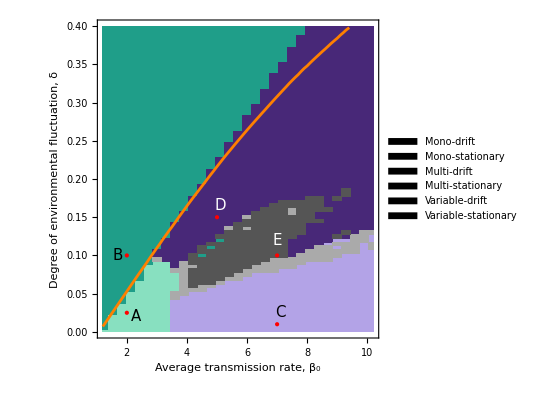

output/figure/Fig6_revise.pdf

```mathematica
(*A.Blue×Yellow*)
colorsA=RGBColor/@{"#A6D5F7","#0072B2","#FFF2A8","#C2A709"};

(*B.Teal×Purple*)
colorsB=RGBColor/@{"#7FDCC0","#1F9E89","#D4A6D8","#7F3C8D"};

(*C.Teal×Indigo*)
colorsC=RGBColor/@{"#88E0C0","#1F9E89","#B3A3E7","#482878",Lighter[Gray],Darker[Gray]};

(*使いたいセットを選ぶ*)
colors=colorsC;  (* ←A/B/C に切替*)
(*colors={RGBColor["#A6D5F7"],(*単峰・停止*)RGBColor["#0072B2"],(*単峰・動く*)RGBColor["#B8DE29"],(*二峰・停止*)RGBColor["#4DAF4A"]  (*二峰・動く*)};*)
ListContourPlot[resultList,InterpolationOrder->0,PlotLegends->SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]],FrameStyle->Directive[Black,12],Contours->{1.5,2.5,3.5,4.5,5.5},ContourShading->colors,FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]}];
ListLinePlot[{criticallisttrue},PlotStyle->{Orange,Red,Blue}];
Show[{%%,%},Epilog->{PointSize->0.02,Red,Point[{{2,0.025},{2,0.1},{7,0.01},{5,0.15},{7,0.1}}],Black,Text[Style["B",15],{1.7,0.1}],Text[Style["A",15],{2.3,0.02}],Text[Style["C",15],{7.1,0.025}],White,Text[Style["D",15],{5.1,0.165}],Text[Style["E",15],{7,0.12}]}]
Rasterize[%,"Image",ImageResolution->300];
 Export["output/figure/Fig6_revise.pdf",%]
```

0.005

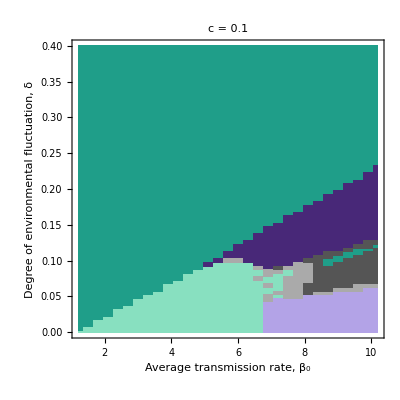

```mathematica
matrixoligomorph=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_c=0.1_morph.csv","Table"];
matrixoligomoved=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_c=0.1_moved.csv","Table"];
   tol=0.005(*0.005;  *)
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[Abs[assoctrait[{z1,z2}]]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[Abs[assoctrait[{z1,z2}]]>TV,3,4],If[Abs[assoctrait[{z1,z2}]]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;

 　 (*A.Blue×Yellow*)
colorsA=RGBColor/@{"#A6D5F7","#0072B2","#FFF2A8","#C2A709"};

(*B.Teal×Purple*)
colorsB=RGBColor/@{"#7FDCC0","#1F9E89","#D4A6D8","#7F3C8D"};

(*C.Teal×Indigo*)
colorsC=RGBColor/@{"#88E0C0","#1F9E89","#B3A3E7","#482878",Lighter[Gray],Darker[Gray]};

(*使いたいセットを選ぶ*)
colors=colorsC;  (* ←A/B/C に切替*)
(*colors={RGBColor["#A6D5F7"],(*単峰・停止*)RGBColor["#0072B2"],(*単峰・動く*)RGBColor["#B8DE29"],(*二峰・停止*)RGBColor["#4DAF4A"]  (*二峰・動く*)};*)
PSA=ListContourPlot[resultList,InterpolationOrder->0,(*PlotLegends->SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]],*)FrameStyle->Directive[Black,12],Contours->{1.5,2.5,3.5,4.5,5.5},ContourShading->colors,PlotRange->All,FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]},PlotLabel->Style["c = 0.1",Black,15]]
```

0.005

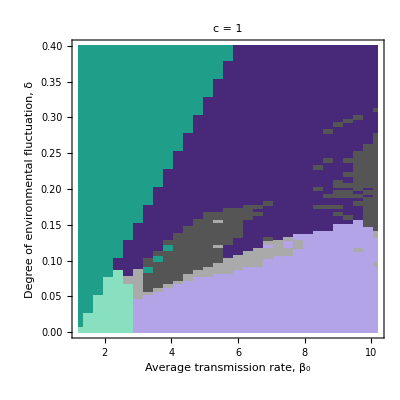

```mathematica
matrixoligomorph=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_c=1_morph.csv","Table"];
matrixoligomoved=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_c=1_moved.csv","Table"];
   tol=0.005(*0.005;  *)
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[Abs[assoctrait[{z1,z2}]]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[Abs[assoctrait[{z1,z2}]]>TV,3,4],If[Abs[assoctrait[{z1,z2}]]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;

 　 (*A.Blue×Yellow*)
colorsA=RGBColor/@{"#A6D5F7","#0072B2","#FFF2A8","#C2A709"};

(*B.Teal×Purple*)
colorsB=RGBColor/@{"#7FDCC0","#1F9E89","#D4A6D8","#7F3C8D"};

(*C.Teal×Indigo*)
colorsC=RGBColor/@{"#88E0C0","#1F9E89","#B3A3E7","#482878",Lighter[Gray],Darker[Gray]};

(*使いたいセットを選ぶ*)
colors=colorsC;  (* ←A/B/C に切替*)
(*colors={RGBColor["#A6D5F7"],(*単峰・停止*)RGBColor["#0072B2"],(*単峰・動く*)RGBColor["#B8DE29"],(*二峰・停止*)RGBColor["#4DAF4A"]  (*二峰・動く*)};*)
PSB=ListContourPlot[resultList,InterpolationOrder->0,(*PlotLegends->SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]],*)FrameStyle->Directive[Black,12],Contours->{1.5,2.5,3.5,4.5,5.5},ContourShading->colors,PlotRange->All,FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]},PlotLabel->Style["c = 1",Black,15]]
```

0.005

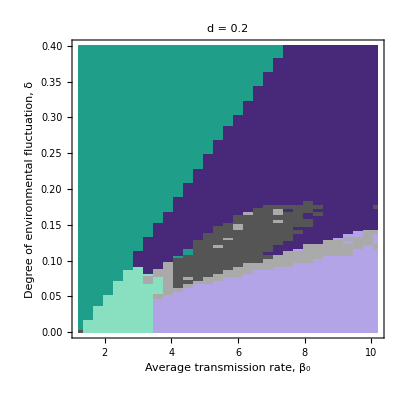

```mathematica
matrixoligomorph=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_d=0.2_morph.csv","Table"];
matrixoligomoved=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_d=0.2_moved.csv","Table"];
   tol=0.005(*0.005;  *)
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[Abs[assoctrait[{z1,z2}]]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[Abs[assoctrait[{z1,z2}]]>TV,3,4],If[Abs[assoctrait[{z1,z2}]]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;

 　 (*A.Blue×Yellow*)
colorsA=RGBColor/@{"#A6D5F7","#0072B2","#FFF2A8","#C2A709"};

(*B.Teal×Purple*)
colorsB=RGBColor/@{"#7FDCC0","#1F9E89","#D4A6D8","#7F3C8D"};

(*C.Teal×Indigo*)
colorsC=RGBColor/@{"#88E0C0","#1F9E89","#B3A3E7","#482878",Lighter[Gray],Darker[Gray]};

(*使いたいセットを選ぶ*)
colors=colorsC;  (* ←A/B/C に切替*)
(*colors={RGBColor["#A6D5F7"],(*単峰・停止*)RGBColor["#0072B2"],(*単峰・動く*)RGBColor["#B8DE29"],(*二峰・停止*)RGBColor["#4DAF4A"]  (*二峰・動く*)};*)
PSC=ListContourPlot[resultList,InterpolationOrder->0,(*PlotLegends->SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]],*)FrameStyle->Directive[Black,12],Contours->{1.5,2.5,3.5,4.5,5.5},ContourShading->colors,PlotRange->All,FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]},PlotLabel->Style["d = 0.2",Black,15]]
```

0.005

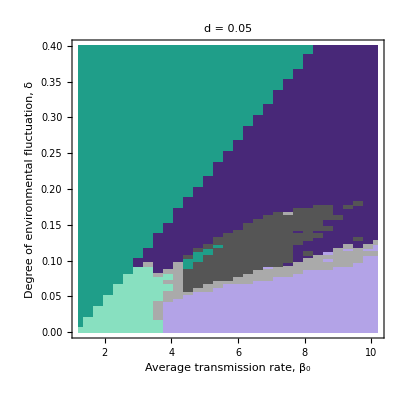

```mathematica
matrixoligomorph=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_d=0.05_morph.csv","Table"];
matrixoligomoved=
Rest@Import["output/oligo_data/traj_for_figure_M2_fast_large_var_detailed2_online_old_d=0.05_moved.csv","Table"];
   tol=0.005(*0.005;  *)
TV=3;
assocmorph=Association[#[[1;;2]]->#[[3]]&/@matrixoligomorph];
assoctrait=Association[#[[1;;2]]->#[[3]]&/@matrixoligomoved];
commonXY=Intersection[Keys[assocmorph],Keys[assoctrait]];
conditionphase[z1_,z2_]:=If[1-tol<assocmorph[{z1,z2}]<1+tol,If[Abs[assoctrait[{z1,z2}]]>TV,1,2],If[2-tol<assocmorph[{z1,z2}]<2+tol,If[Abs[assoctrait[{z1,z2}]]>TV,3,4],If[Abs[assoctrait[{z1,z2}]]>TV,5,6]]]
resultList={#1,#2,conditionphase[#1,#2]}&@@@commonXY;

 　 (*A.Blue×Yellow*)
colorsA=RGBColor/@{"#A6D5F7","#0072B2","#FFF2A8","#C2A709"};

(*B.Teal×Purple*)
colorsB=RGBColor/@{"#7FDCC0","#1F9E89","#D4A6D8","#7F3C8D"};

(*C.Teal×Indigo*)
colorsC=RGBColor/@{"#88E0C0","#1F9E89","#B3A3E7","#482878",Lighter[Gray],Darker[Gray]};

(*使いたいセットを選ぶ*)
colors=colorsC;  (* ←A/B/C に切替*)
(*colors={RGBColor["#A6D5F7"],(*単峰・停止*)RGBColor["#0072B2"],(*単峰・動く*)RGBColor["#B8DE29"],(*二峰・停止*)RGBColor["#4DAF4A"]  (*二峰・動く*)};*)
PSD=ListContourPlot[resultList,InterpolationOrder->0,(*PlotLegends->SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]],*)FrameStyle->Directive[Black,12],Contours->{1.5,2.5,3.5,4.5,5.5},ContourShading->colors,PlotRange->All,FrameLabel->{Style["Average transmission rate, β_0",15],Style["Degree of environmental fluctuation, δ",15]},PlotLabel->Style["d = 0.05",Black,15]]
```

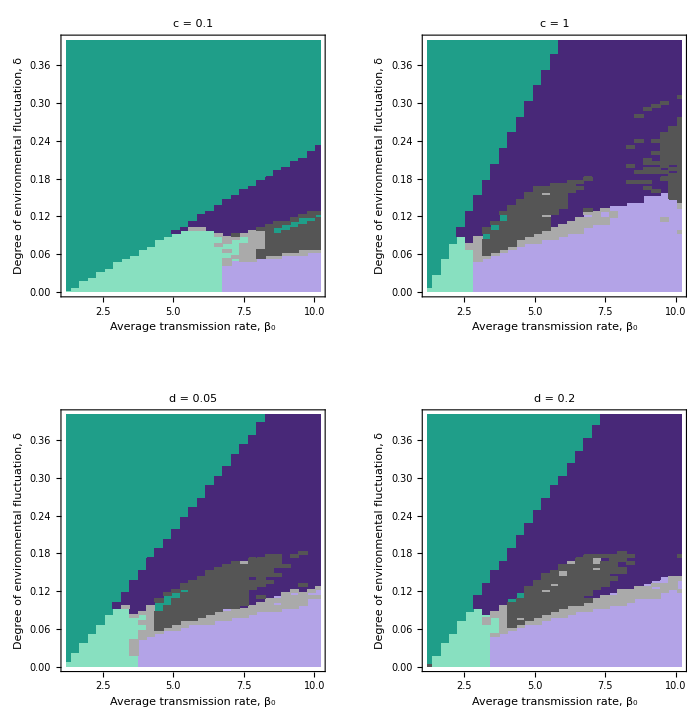

-Graphics-

output/figure/FigSupplementary_revise.pdf

```mathematica
PSL=SwatchLegend[colorsC,{"Mono-drift","Mono-stationary","Multi-drift","Multi-stationary","Variable-drift","Variable-stationary"},LegendMarkerSize->20,LegendMarkers->Graphics[Rectangle[]]]
GraphicsGrid[{{PSA,PSB},{PSD,PSC}},ImageSize->700]
Labeled[%,PSL,Right,Spacings->2]
Rasterize[%,"Image",ImageResolution->300];
 Export["output/figure/FigSupplementary_revise.pdf",%]
```